117.748+2. (100.531-1. Vk$4439)

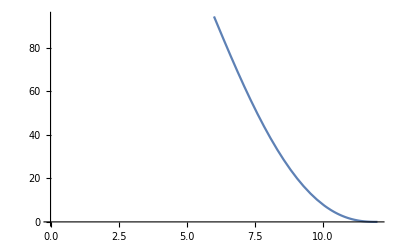

```mathematica
(*If[condition, true, false]*)
BritiPytt[R_,L_,l_,H_]:= Module[{Vs,Vk},
Vs=π*R^2*L/2+R^2*ArcSin[(H-R)/R]+(H-R)*Sqrt[2*H*R-H^2];If[H≤R,d=R-H;If[d==0,Vk=l/3*(-2*d*Sqrt[R^2-d^2]+d^3/R*Log[Sqrt[R^2-d^2]+R]+R^2*ArcCos[d/R]-0);N[Vs+2*Vk]],If[d>0,Vk=l/3*(-2*d*Sqrt[R^2-d^2]+d^3/R*Log[Sqrt[R^2-d^2]+R]+R^2*ArcCos[d/R]-d^3/R*Log[d]);N[Vs+2*Vk]]];If[H>R,d=H-R;Vk=l/3*(-2*d*Sqrt[R^2-d^2]+d^3/R*Log[Sqrt[R^2-d^2]+R]+R^2*ArcCos[d/R]-d^3/R*Log[d]),N[Vs+2*(π*R^2*l/3-Vk)]
]]


BritiPytt[4,5,6,3]
Plot[BritiPytt[6,20,5,h],{h,0,12}]
```